```mathematica
total1=Length[Con1];
M=Table[Con1[[i]][[3]], {i,total1}]
Sig=Table[Con1[[i]][[4]], {i,total1}]
xi=Table[Con1[[i]][[9]], {i,total1}]
```

{0.0277245039027649372134608007229883,0.0458205254671695821590956304232744,0.0692717979656480329163077385143762,0.0931678171269177432129961034576811,0.11731345089274758313734529288513,0.166033524774724019110409508341608,0.21508824397530548405637621289379,0.26434316799617060987608630435799,0.30433947524736060633683466884055,0.31373150006131405987453815388651,0.36321505540406058625671037913288,0.41276990653178474055317276329427,0.4623800552191146538337240216505,0.51203426437152537699533408590146,0.56172439442229438920034453797152,0.61144426972096206094002751126243,0.66118918206437182829940257766151,0.71095542401390484265812607002503,0.76074003367304825554327800562798,0.81054060912304065683337609759715,0.86035517673646917233761333900032,0.91018209712181578675474165645111,0.96001999237788144399596956781069,1.009867697024326716854145801074,1.0597242147891411362493062046586,1.1095886881916020546191039317672,1.1594603752076232994099233397416,1.2093386290413467122956681720781,1.259222882919334052199834128138,1.309112637640903444605631885477,1.3590074514388622201262776972561,1.4089069316368830419158018745552,1.4588107277784969431966419030174,1.5087185258843674821642301216666,1.5586300436782308521656332213433,1.6085450265005106610074504649402,1.6584632439222797564801922060998,1.708384486814961148499789807931,1.758308564855638464804666778742,1.808235304385323076216006259392,1.858164546558080340214469045279,1.908096145720863947486992532159,1.958029968055630126055800001867,2.0079658903365988856523868588,3.506656254372791479253502220761,4.006373432128329347152040349477,4.011370838765053541189226455513,7.005305122334903551651390352465}

{0.19718844383335259924771333671,0.2557183720800904764952054623,0.29978843812835482240586587164,0.32681110221446421472708994896,0.34487226881891270529430203478,0.36830920512060715624927903762,0.38400002689359205961416152494,0.39608931145867293294510722031,0.40436613475645584498240310442,0.40616860857662707685727146505,0.41497364403922590197504631194,0.42289686133619211284651204609,0.43017583735270532713845411278,0.43707320607692819250340282484,0.4433265456989843955592707011,0.44937206566392570606620667595,0.45513357184505450344372146262,0.46065288653898331596103785951,0.46596122062672622916950921946,0.4710821546534510342851722991,0.47603670347514576014410324831,0.48083508359375987153660429883,0.48550009368058245008443546701,0.49003542136933305845442398949,0.49445206201471588631048796511,0.49876251140457464984773249323,0.50297213306442304413099549892,0.50708755378298248466229422543,0.51111465707427143580566856391,0.51505870376875687390022112486,0.5189244220544508733260625177,0.52271608470259515647384817709,0.52643756800844188381155965016,0.53009240667993154332590022688,0.53368383244873466649502989249,0.53721481547906375885221842483,0.54068809165627035143531830731,0.54410618678979103210888389854,0.54747144561028219485017143108,0.55078604183057751470731082376,0.55405200292549610492563440682,0.5572712199737789253543614919,0.56044546141737853723861473281,0.56357638418315231126672230522,0.64280277263214886338025062132,0.66476951425937723097848758694,0.66498100295283301240200665622,0.77140603365157258501580985218}

{0.0087731438546566246671103356726,0.045787151626028636455271192275,0.093282247740728775044880520472,0.14126887911209894485256803505,0.18960674365996484934606404434,0.28704360538366269324987885605,0.38515804039864759528829507585,0.48370928314740378235722167501,0.56376212171746837232839235588,0.58256352682800530262964151312,0.68164068847195720601731821966,0.78088930401627473326325243928,0.88027434500511272484753990286,0.97977071900408808677619885922,1.079360415820550556607989007,1.1790289625799164300700109412,1.2787655549431928573464703907,1.3785614579811282787352733197,1.4784096109152755782436633158,1.5783041671650065493702830065,1.6782402932425320782957532861,1.7782138868543697089257172518,1.8782214561311869347947838793,1.9782600094545814391987349652,2.0783269284758341851367270004,2.1784199852556889413701928338,2.2785371650625148438797155944,2.3786766332470616311998910869,2.4788369627164969686299100072,2.579016713747530496351234918,2.6792145063136805804316695035,2.7794293442763136338466680111,2.8796601909277020899696343566,2.9799060899540582122882824671,3.0801661609746978666492159971,3.1804397237016998234172334272,3.2807260232206681243333237366,3.381024308466532445225637154,3.4813342136324774387508270201,3.5816550137008869521878539445,3.6819861015577739920962977252,3.7823272947090106690630757696,3.8826779954942566354790440704,3.9830376827586402016957433743,6.996760960993385456072343126,8.0021707935473314781140974501,8.0122266588960486285521456245,14.038943386718578165652678981}

```mathematica
MS1=Table[{Con1[[i]][[1]]^2 Pi,Con1[[i,3]]}, {i,total1}]
```

{{0.000314159,0.0277245039027649372134608007229883},{0.00785398,0.0458205254671695821590956304232744},{0.0314159,0.0692717979656480329163077385143762},{0.0706858,0.0931678171269177432129961034576811},{0.125664,0.11731345089274758313734529288513},{0.282743,0.166033524774724019110409508341608},{0.502655,0.21508824397530548405637621289379},{0.785398,0.26434316799617060987608630435799},{1.06048,0.30433947524736060633683466884055},{1.13097,0.31373150006131405987453815388651},{1.53938,0.36321505540406058625671037913288},{2.01062,0.41276990653178474055317276329427},{2.54469,0.4623800552191146538337240216505},{π,0.51203426437152537699533408590146},{3.80133,0.56172439442229438920034453797152},{4.52389,0.61144426972096206094002751126243},{5.30929,0.66118918206437182829940257766151},{6.15752,0.71095542401390484265812607002503},{7.06858,0.76074003367304825554327800562798},{8.04248,0.81054060912304065683337609759715},{9.0792,0.86035517673646917233761333900032},{10.1788,0.91018209712181578675474165645111},{11.3411,0.96001999237788144399596956781069},{4 π,1.009867697024326716854145801074},{13.8544,1.0597242147891411362493062046586},{15.2053,1.1095886881916020546191039317672},{16.619,1.1594603752076232994099233397416},{18.0956,1.2093386290413467122956681720781},{19.635,1.259222882919334052199834128138},{21.2372,1.309112637640903444605631885477},{22.9022,1.3590074514388622201262776972561},{24.6301,1.4089069316368830419158018745552},{26.4208,1.4588107277784969431966419030174},{28.2743,1.5087185258843674821642301216666},{30.1907,1.5586300436782308521656332213433},{32.1699,1.6085450265005106610074504649402},{34.2119,1.6584632439222797564801922060998},{36.3168,1.708384486814961148499789807931},{38.4845,1.758308564855638464804666778742},{40.715,1.808235304385323076216006259392},{43.0084,1.858164546558080340214469045279},{45.3646,1.908096145720863947486992532159},{47.7836,1.958029968055630126055800001867},{16 π,2.0079658903365988856523868588},{49 π,3.506656254372791479253502220761},{64 π,4.006373432128329347152040349477},{201.565,4.011370838765053541189226455513},{196 π,7.005305122334903551651390352465}}

```mathematica
MR1= Table[{Con1[[i]][[1]],Con1[[i,3]]},{i,total1}]
MΣ1=Table[{Con1[[i]][[1]],Con1[[i]][[4]]},{i,total1}]
```

{{0.01,0.0277245039027649372134608007229883},{0.05,0.0458205254671695821590956304232744},{0.1,0.0692717979656480329163077385143762},{0.15,0.0931678171269177432129961034576811},{0.2,0.11731345089274758313734529288513},{0.3,0.166033524774724019110409508341608},{0.4,0.21508824397530548405637621289379},{0.5,0.26434316799617060987608630435799},{0.581,0.30433947524736060633683466884055},{0.6,0.31373150006131405987453815388651},{0.7,0.36321505540406058625671037913288},{0.8,0.41276990653178474055317276329427},{0.9,0.4623800552191146538337240216505},{1,0.51203426437152537699533408590146},{1.1,0.56172439442229438920034453797152},{1.2,0.61144426972096206094002751126243},{1.3,0.66118918206437182829940257766151},{1.4,0.71095542401390484265812607002503},{1.5,0.76074003367304825554327800562798},{1.6,0.81054060912304065683337609759715},{1.7,0.86035517673646917233761333900032},{1.8,0.91018209712181578675474165645111},{1.9,0.96001999237788144399596956781069},{2,1.009867697024326716854145801074},{2.1,1.0597242147891411362493062046586},{2.2,1.1095886881916020546191039317672},{2.3,1.1594603752076232994099233397416},{2.4,1.2093386290413467122956681720781},{2.5,1.259222882919334052199834128138},{2.6,1.309112637640903444605631885477},{2.7,1.3590074514388622201262776972561},{2.8,1.4089069316368830419158018745552},{2.9,1.4588107277784969431966419030174},{3.,1.5087185258843674821642301216666},{3.1,1.5586300436782308521656332213433},{3.2,1.6085450265005106610074504649402},{3.3,1.6584632439222797564801922060998},{3.4,1.708384486814961148499789807931},{3.5,1.758308564855638464804666778742},{3.6,1.808235304385323076216006259392},{3.7,1.858164546558080340214469045279},{3.8,1.908096145720863947486992532159},{3.9,1.958029968055630126055800001867},{4,2.0079658903365988856523868588},{7,3.506656254372791479253502220761},{8,4.006373432128329347152040349477},{8.01,4.011370838765053541189226455513},{14,7.005305122334903551651390352465}}

{{0.01,0.19718844383335259924771333671},{0.05,0.2557183720800904764952054623},{0.1,0.29978843812835482240586587164},{0.15,0.32681110221446421472708994896},{0.2,0.34487226881891270529430203478},{0.3,0.36830920512060715624927903762},{0.4,0.38400002689359205961416152494},{0.5,0.39608931145867293294510722031},{0.581,0.40436613475645584498240310442},{0.6,0.40616860857662707685727146505},{0.7,0.41497364403922590197504631194},{0.8,0.42289686133619211284651204609},{0.9,0.43017583735270532713845411278},{1,0.43707320607692819250340282484},{1.1,0.4433265456989843955592707011},{1.2,0.44937206566392570606620667595},{1.3,0.45513357184505450344372146262},{1.4,0.46065288653898331596103785951},{1.5,0.46596122062672622916950921946},{1.6,0.4710821546534510342851722991},{1.7,0.47603670347514576014410324831},{1.8,0.48083508359375987153660429883},{1.9,0.48550009368058245008443546701},{2,0.49003542136933305845442398949},{2.1,0.49445206201471588631048796511},{2.2,0.49876251140457464984773249323},{2.3,0.50297213306442304413099549892},{2.4,0.50708755378298248466229422543},{2.5,0.51111465707427143580566856391},{2.6,0.51505870376875687390022112486},{2.7,0.5189244220544508733260625177},{2.8,0.52271608470259515647384817709},{2.9,0.52643756800844188381155965016},{3.,0.53009240667993154332590022688},{3.1,0.53368383244873466649502989249},{3.2,0.53721481547906375885221842483},{3.3,0.54068809165627035143531830731},{3.4,0.54410618678979103210888389854},{3.5,0.54747144561028219485017143108},{3.6,0.55078604183057751470731082376},{3.7,0.55405200292549610492563440682},{3.8,0.5572712199737789253543614919},{3.9,0.56044546141737853723861473281},{4,0.56357638418315231126672230522},{7,0.64280277263214886338025062132},{8,0.66476951425937723097848758694},{8.01,0.66498100295283301240200665622},{14,0.77140603365157258501580985218}}

```mathematica
repxy1=FindFit[Table[{M[[i]], Sig[[i]], xi[[i]]}, {i,1,total1}],{a x + b y}, {x,y}, {a,b}]
```

{x→2.0185273546624032501647025047,y→-0.1257495646151513231838916156}

```mathematica
Table[(-xi[[i]]+x  M[[i]]+y Sig[[i]])/xi[[i]]/.{x->3/23 (7+6 √2),y->1/23 (3-4 √2)},{i,1,total1}]
```

{2.786577137619370029634502119,0.3761452567440075665724343516,0.1286856364059931008237688098,0.0648519413439290378875608661,0.039593375057468359398397404,0.0200970443416120836386515226,0.0127828839572395686377965941,0.00922400294633432900980686245,0.00751755084243945930390621306,0.00720725671485069559415397886,0.005944842635976191225236496,0.0050970382438563696486617115,0.0044961938440400465535133123,0.00403899417125811009579621989,0.0037154582324561836749555858,0.0034507933611794069941894379,0.00323920576655269573470659,0.0030666259387973462526746115,0.0029234800199447820572388276,0.0028031110700069599609311606,0.0027005278642452992627110164,0.002612526099701702695462055,0.0025357625288794443749809985,0.0024686474119092597413289512,0.0024094740039152525436450758,0.0023567176721879872022387418,0.0023094911301242779619746286,0.0022669995827778102551379855,0.0022285113238538854566839065,0.0021934937382074886083807095,0.0021615375671981929818090891,0.0021322085654191631091413156,0.002105192430415177816073519,0.0020802279607823701326878148,0.0020570953126269196389828186,0.0020355662831197651177861604,0.0020154864686524774969615929,0.0019967384938562274472579631,0.0019791245009327067863662824,0.0019625841682304333840769494,0.001947044345205188250594415,0.0019323383456422245567150037,0.001918433635728883176608186,0.0019052903012384041780038752,0.0016861278084690688386542483,0.0016481163711562916012368068,0.0016477406499700565761225832}

```mathematica
Table[(-xi[[i]]+x  M[[i]]+y Sig[[i]])/xi[[i]]/.repxy1,{i,1,total1}]
```

{2.508502490050246989700573154,0.306967102191906351870641428,0.0888144864211014929014629755,0.0361036119003052199374728718,0.0169521840923109148257527619,0.004070979652563563210602824,0.000288935836157914425645483,-0.001071067407022307020941279,-0.0015235118978282901804527834,-0.0015862714020440418789091953,-0.0017573030673119013853864323,-0.0017753412953202143290320483,-0.0017235995271433542624592533,-0.001655192544868637858291293,-0.0015422393141655283588551657,-0.001441669273683346578380663,-0.001341986319431368669105669,-0.001245993444541562394905848,-0.00115492904353655315984217,-0.001069149550625292854088385,-0.0009888167174334474136873305,-0.0009133092371688846309022118,-0.0008430367326982782551275549,-0.0007771258506505855190378534,-0.0007153351215512746678755506,-0.0006576052932169356432838024,-0.0006034780538203765257693449,-0.0005526345415168368616922458,-0.0005048678896072869863166238,-0.0004599144345206362814551613,-0.0004175032896792597106268944,-0.0003774838922942325245140096,-0.0003396652031036836927065573,-0.0003038693552839575527156865,-0.0002699328163394278119839015,-0.0002377474345349425004326666,-0.0002071714229572422595702498,-0.0001780602247252236109901071,-0.000150378974253297412089766,-0.000123980893313996042223658,-0.0000987539723381962747655294,-0.0000746986522826850580622225,-0.0000516981900685220420296389,-0.0000296578357814486315349772,0.0003635694016181951362970491,0.0004341312685575728255264725,0.0004347165060102329770872725}

```mathematica
MPS=Table[{Con1[[i,1]],(x  M[[i]]+y Sig[[i]])/.{x->3/23 (7+6 √2),y->1/23 (3-4 √2)}},{i,44}];
```

```mathematica
MPS=Table[{Con1[[i,1]],(x  M[[i]]+y Sig[[i]])/.repxy1},{i,1,48}];
```

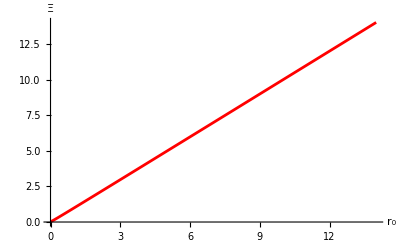

```mathematica
MPSplot=ListPlot[MPS,Joined->True,PlotRange->All,PlotStyle->Red,AxesLabel->{Style[" r_0",FontSize->18],Style["Ξ",FontSize->18]}]
```

```mathematica
XIR=Join[Table[{Con1[[i,1]],xi[[i]]},{i,1,42,3}],Table[{Con1[[i,1]],xi[[i]]},{i,44,48}]];
```

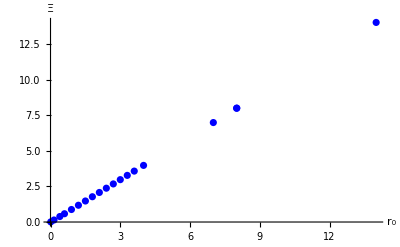

```mathematica
XIplot=ListPlot[XIR,PlotRange->All,PlotStyle->Blue,AxesLabel->{Style[" r_0",FontSize->18],Style["Ξ",FontSize->18]}]
```

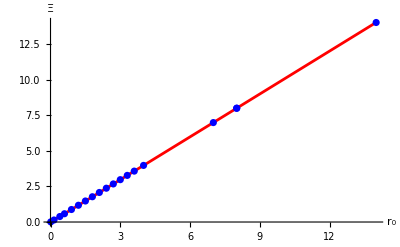

```mathematica
Show[MPSplot,XIplot]
```

```mathematica
Table[(-xi[[i]]+x  M[[i]]+y Sig[[i]])/xi[[i]]/.{x->3/23 (7+6 √2),y->1/23 (3-4 √2)},{i,1,total1}]
```

{2.786577137619370029634502119,0.3761452567440075665724343516,0.1286856364059931008237688098,0.0648519413439290378875608661,0.039593375057468359398397404,0.0200970443416120836386515226,0.0127828839572395686377965941,0.00922400294633432900980686245,0.00751755084243945930390621306,0.00720725671485069559415397886,0.005944842635976191225236496,0.0050970382438563696486617115,0.0044961938440400465535133123,0.00403899417125811009579621989,0.0037154582324561836749555858,0.0034507933611794069941894379,0.00323920576655269573470659,0.0030666259387973462526746115,0.0029234800199447820572388276,0.0028031110700069599609311606,0.0027005278642452992627110164,0.002612526099701702695462055,0.0025357625288794443749809985,0.0024686474119092597413289512,0.0024094740039152525436450758,0.0023567176721879872022387418,0.0023094911301242779619746286,0.0022669995827778102551379855,0.0022285113238538854566839065,0.0021934937382074886083807095,0.0021615375671981929818090891,0.0021322085654191631091413156,0.002105192430415177816073519,0.0020802279607823701326878148,0.0020570953126269196389828186,0.0020355662831197651177861604,0.0020154864686524774969615929,0.0019967384938562274472579631,0.0019791245009327067863662824,0.0019625841682304333840769494,0.001947044345205188250594415,0.0019323383456422245567150037,0.001918433635728883176608186,0.0019052903012384041780038752,0.0016861278084690688386542483,0.0016481163711562916012368068,0.0016477406499700565761225832}